```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

generic model {Lorentz} initialized

classes model {../Models/SMS-stop_SMQCD/SMS-stop_SMQCD} initialized

in total: 1 Particles insertion

in total: 1 Particles amplitude

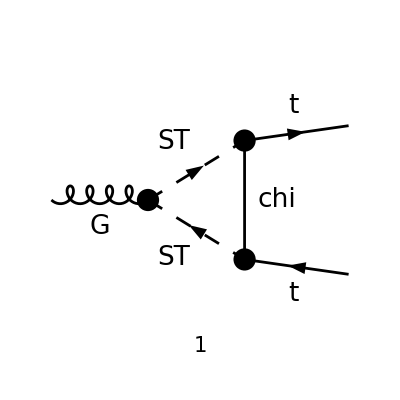

```mathematica
SetDirectory[NotebookDirectory[]];
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../Models/SMS-stop_SMQCD/SMS-stop_SMQCD",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { V[1]} -> {F[3],-F[3]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->True,DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[!M==={0},AppendTo[nonZero,n]];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 300,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{k},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings]
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)
```

in total: 1 Particles amplitude

(2 √π √aS T_Col2Col3^Glu1 (p1+p2-2 q)^μ (-ⅈ yDM (γ̄)^7).(mChi+γ·(p1-q)).(-ⅈ yDM (γ̄)^6))/((q^2-mST^2).((q-p1)^2-mChi^2).((-p1-p2+q)^2-mST^2))

-(2 √π √aS yDM^2 T_Col2Col3^Glu1 (p1^μ+p2^μ-2 q^μ) ((γ·p1).(γ̄)^6-(γ·q).(γ̄)^6))/((q^2-mST^2).((p1-q)^2-mChi^2).((p1+p2-q)^2-mST^2))

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_2(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_22(p1^2,2 (p1·p2)+p1^2+p2^2,p2^2,mChi^2,mST^2,mST^2))

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampC//Simplify
```

-2 ⅈ π^(5/2) √aS yDM^2 T_Col2Col3^Glu1 (2 γ^μ.(γ̄)^6 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+(p1^μ-p2^μ) (γ·p1).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-(p1^μ-p2^μ) (γ·p2).(γ̄)^6 C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p1^μ (γ·p1).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 p2^μ (γ·p2).(γ̄)^6 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)-2 (p1^μ (γ·p2).(γ̄)^6+p2^μ (γ·p1).(γ̄)^6) C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))

```mathematica
ampD=Expand[Collect[(ampC)/.{aS->GS^2/(4 Pi)},{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},foo]]/.foo->FullSimplify
```

-2 ⅈ π^2 √(GS^2) yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1 C_00(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+ⅈ π^2 √(GS^2) yDM^2 p2^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))-ⅈ π^2 √(GS^2) yDM^2 p1^μ T_Col2Col3^Glu1 ((γ·p1).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_11(MT^2,s,MT^2,mChi^2,mST^2,mST^2))-(γ·p2).(γ̄)^6 (C_1(MT^2,s,MT^2,mChi^2,mST^2,mST^2)+2 C_12(MT^2,s,MT^2,mChi^2,mST^2,mST^2)))

```mathematica
UVpart = DiracSimplify[PaXEvaluateUV[ampD,PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon)]]
```

-(ⅈ √(GS.GS) yDM^2 γ^μ.(γ̄)^6 T_Col2Col3^Glu1)/(32 π^2 ε_UV)

```mathematica
PaXEvaluate[PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]+2 PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}]]
```

PaXEvaluate::C0D0: The explicit result for the occurring C0 function(s) is expected to be very complicated. Please rerun PaXEvaluate with the option PaXC0Expand->True to show the result nevertheless. Please set $FCAdvice=False if you do not want to see this message in future.

-1/(2 MT^2 (4 MT^2-s)^2 s^2)(8 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^8-16 s MT^6-16 mChi^2 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^6-16 mST^2 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^6-4 s log(mChi^2/mST^2) MT^6-8 √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^6+12 s^2 MT^4+16 mChi^2 s MT^4-16 mST^2 s MT^4-2 s^3 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4+16 mChi^2 s^2 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4+8 mST^2 s^2 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4+8 mChi^4 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4+8 mST^4 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4-16 mChi^2 mST^2 s C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^4+2 s^2 log(mChi^2/mST^2) MT^4+8 mChi^2 s log(mChi^2/mST^2) MT^4+8 mST^2 s log(mChi^2/mST^2) MT^4+8 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST)) MT^4+8 mChi^2 √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^4-8 mST^2 √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^4+4 s √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^4-2 s^3 MT^2-4 mChi^2 s^2 MT^2+4 mST^2 s^2 MT^2-6 mChi^2 s^3 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^2+2 mST^2 s^3 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^2-8 mChi^4 s^2 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^2-8 mST^4 s^2 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^2+16 mChi^2 mST^2 s^2 C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2) MT^2-s^3 log(mChi^2/mST^2) MT^2-4 mChi^2 s^2 log(mChi^2/mST^2) MT^2-4 mChi^4 s log(mChi^2/mST^2) MT^2-4 mST^4 s log(mChi^2/mST^2) MT^2+8 mChi^2 mST^2 s log(mChi^2/mST^2) MT^2-4 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s^2 log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST)) MT^2+8 mChi^2 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST)) MT^2-8 mST^2 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST)) MT^2-2 s^2 √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^2-8 mChi^2 s √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^2+8 mST^2 s √(s (s-4 mST^2)) log((2 mST^2-s+√(s (s-4 mST^2)))/(2 mST^2)) MT^2-mChi^2 s^3 log(mChi^2/mST^2)+mST^2 s^3 log(mChi^2/mST^2)-2 mChi^4 s^2 log(mChi^2/mST^2)-2 mST^4 s^2 log(mChi^2/mST^2)+4 mChi^2 mST^2 s^2 log(mChi^2/mST^2)+2 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s^3 log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST))+4 mChi^2 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s^2 log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST))-4 mST^2 √(mChi^4-2 mST^2 mChi^2-2 MT^2 mChi^2+mST^4+MT^4-2 mST^2 MT^2) s^2 log((mChi^2+mST^2-MT^2+√(mChi^4-2 (mST^2+MT^2) mChi^2+(mST^2-MT^2)^2))/(2 mChi mST)))

```mathematica
FullSimplify[%,Assumptions->{mST>mChi,mST>MT,MT>0,mChi>0,mST>0}]
```

1/(2 MT^2 s^2 (s-4 MT^2)^2)(-2 MT^2 s (mChi^2 (8 s (mST^2+MT^2)-8 MT^2 (mST^2+MT^2)-3 s^2)+4 mChi^4 (MT^2-s)+(mST-MT) (mST+MT) (4 mST^2 (MT^2-s)-4 MT^4+s^2)) C_0(MT^2,MT^2,s,mST^2,mChi^2,mST^2)+2 MT^2 (√(s (s-4 mST^2)) (log(1/2 (√(s (s-4 mST^2))-s)+mST^2)-2 log(mST)) (-2 s (-2 mChi^2+2 mST^2+MT^2)+4 MT^2 (-mChi^2+mST^2+MT^2)+s^2)+s (4 MT^2-s) (-2 mChi^2+2 (mST^2+MT^2)-s))+2 s log(mChi/mST) (mChi^2 (-4 mST^2 (2 MT^2+s)+4 MT^2 s-8 MT^4+s^2)+2 mChi^4 (2 MT^2+s)+(mST-MT) (mST+MT) (2 mST^2 (2 MT^2+s)+2 MT^2 s-4 MT^4-s^2))-2 s √((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT)) (-2 s (-mChi^2+mST^2+MT^2)+4 MT^2 (mChi^2-mST^2+MT^2)+s^2) (log(mChi^2+√((mChi-mST-MT) (mChi+mST-MT) (mChi-mST+MT) (mChi+mST+MT))+mST^2-MT^2)-log(2 mChi mST)))